```mathematica
SetDirectory["/Users/elias/Desktop/School/SLAC_SULI/for-fitting"];
```

```mathematica
Loading[a_]:=(
c={};
b=Import[a,"Table"];
c=b;
table={};
data={};
Δt={};
ΔF={};
(*NegativeDetected=0*)
Do[
If[Head[c[[i,1]]]==Real,{

time=c[[i,1]];
(*
If[time<0|| NegativeDetected > 0, 
(*shift everything if a negative value detected*)
Print[time]
time=time+100; NegativeDetected=1;
Print[time];
]
*)
If[time>0,
logtime=Log[10,time];
(*logerrorontime=((c⟦i,2⟧-c⟦i,3⟧)/(2*1.65))/(time*Log[10]);*)
flux=c⟦i,2⟧;
logflux=Log[10,c⟦i,2⟧];

(*logfluxerror=((c⟦i,5⟧-c⟦i,6⟧)/(2*1.65))/(c[[i,4]]*Log[10]);*)
logfluxerror=c[[i,3]];


If[flux>0,AppendTo[table,{logtime,logerrorontime,logflux,logfluxerror}]];
If[flux>0,AppendTo[data,{logtime,logflux}]];
If[flux>0,AppendTo[Δt,logerrorontime]];
If[flux>0,AppendTo[ΔF,logfluxerror]];

(*If[flux>0,If[(time<10^2.5||time>10^3),AppendTo[table,{logtime,logerrorontime,logflux,logfluxerror}]]];

		If[flux>0,If[time>10^2.5 && time<10^3 && flux<2 && flux>0,AppendTo[table,{logtime,logerrorontime,logflux,logfluxerror}]]];

If[flux>0,If[time<10^2.5||time>10^3,AppendTo[data,{logtime,logflux}]]];

		If[flux>0,If[time>10^2.5 && time<10^3 && flux<2 && flux>0, AppendTo[data,{logtime,logflux}]]];

If[flux>0,If[time<10^2.5||time>10^3,AppendTo[Δt,logerrorontime]]];
	      
If[flux>0,If[time>10^2.5 && time<10^3 && flux<2 && flux>0, AppendTo[Δt,logerrorontime]]];

If[flux>0,If[time<10^3.5||time>10^4.7,AppendTo[ΔF,logfluxerror]]];

If[flux>0,If[time>10^2.5 && time<10^3.7 && flux<2 && flux>0, AppendTo[ΔF,logfluxerror]]];*)





]}
]
,{i,1,Length[c]}];
)
```

```mathematica
Division[start_,end_]:=
(
startp=start ;(*by default,it means that we start from the beginning*)
endp=end; (*manually*)
Part1={};
Δt1={};
ΔF1={};

Part2={};
Δt2={};
ΔF2={};

Do[If[startp≤data[[i,1]]≤endp,
(
AppendTo[Part1,data[[i]]];
AppendTo[Δt1,Δt[[i]]];
AppendTo[ΔF1,ΔF[[i]]];
),
(
AppendTo[Part2,data[[i]]];
AppendTo[Δt2,Δt[[i]]];
AppendTo[ΔF2,ΔF[[i]]];
)
],{i,1,Length[data]}];
);
```

```mathematica
model[F_,T_,α_,t_]:=Piecewise[{{Log[10,10^F*Exp[α-(10^x*α/10^T)]*Exp[-Abs[t]/10^x]],10^x<10^T},{Log[10,10^F*(10^x/10^T)^(-α)*Exp[-Abs[t]/10^x]],10^x≥10^T}}];
```

```mathematica
fitowanie[a_,b_,c_,d_,er_,datapart_,beg_,end_]:=
(
fit1=NonlinearModelFit[datapart,model[F,T,α,t],{{F,a},{T,b},{α,c},{t,d}},x,Weights->1/er^2];
bestparameters=fit1["BestFitParameters"];
besterrors=fit1["ParameterErrors"];
Print["----------------------------------------------"];
Print["best fit parameters: ",bestparameters];
Print["theirs errors: ",besterrors];
Print["confidence intervals: ",fit1["ParameterConfidenceIntervals",ConfidenceLevel->0.68]];


(*if Subscript[t, a] is <0 we have to fix it and refit in order for following Δχ^2 calculations*)
If[fit1["BestFitParameters"][[4,2]]≤0,
(
Clear[bestparameters];
startowe={{F,a},{T,b},{α,c}};
fit1=NonlinearModelFit[datapart,model[F,T,α,0],startowe,x,Weights->1/er^2];
bestparameters=fit1["BestFitParameters"];
besterrors=fit1["ParameterErrors"];
zamiana[i_,k_]:={parametr[[i]]->FaTaTable[[i,k]],t->0};
start={{F,#[[1,2]]},{T,#[[2,2]]},{α,#[[3,2]]}}&[bestparameters];
Flux=model[F,T,α,0]/.bestparameters;
Print["!!!!!!!!!!!!!!!!!!! changing best fit parameters to: ",bestparameters," with fixed ta->0"];
Print["best fit parameters: ",bestparameters];
Print["theirs errors: ",besterrors];
Print["confidency intervals: ",fit1["ParameterConfidenceIntervals",ConfidenceLevel->0.68]];
),
(
zamiana[i_,k_]:={parametr[[i]]->FaTaTable[[i,k]]};
start={{F,#[[1,2]]},{T,#[[2,2]]},{α,#[[3,2]]},{t,#[[4,2]]}}&[bestparameters];
Flux=model[F,T,α,t]/.bestparameters
)
];
Print[
Show[
Plot[model[F,T,α,t]/.bestparameters/.t->0,{x,beg,end}],ListPlot[datapart,PlotRange->All],ListPlot[{{bestparameters[[2]][[2]],bestparameters[[1]][[2]]}},PlotStyle->{Green, PointSize[0.05]},PlotRange->All],
PlotRange->All,FrameLabel->{"log time rest frame (s)","log Flux (erg s^-1)"}]]
Print["----------------------------------------------"];
Clear[fit1];
)
```

```mathematica
Cuts[a_,b_]:=
(
compartmentT:=Interval[{a[[1]],b[[1]]}];
compartmentF:=Interval[{a[[2]],b[[2]]}];
Do[
If[!IntervalMemberQ[compartmentT,data[[i,1]]]||!IntervalMemberQ[compartmentF,data[[i,2]]],
(
AppendTo[Part12,data[[i]]];
AppendTo[Δt12,Δt[[i]]];
AppendTo[ΔF12,ΔF[[i]]];
)
];

,{i,1,Length[data]}];

data=Part12;
Δt=Δt12;
ΔF=ΔF12;

Part12={};
Δt12={};
ΔF12={};

)
```

```mathematica
Chisquare[datapart_,er_]:=Module[{ν,REDUCED},


singleχ[j_]:=((datapart[[j,2]]-Flux/.x->datapart[[j,1]])/er[[j]])^2;

bestfitχ=Sum[singleχ[j],{j,1,Length[datapart]}];
REDUCED=bestfitχ/(Length[datapart]-3);
ν=Length[datapart];
X=REDUCED ν;
PROBABILITY=2^(-ν/2)/Gamma[ν/2] NIntegrate[ⅇ^(-x/2) x^(-1+ν/2),{x,X,Infinity}];
Print["GRB ",id," afterglow has"," χ^2: ",bestfitχ," and  reduced χ^2: ",REDUCED," α: ",Chop[PROBABILITY]];
];
```

```mathematica
IntervalEstimating[b_,e_,s_,datapart_,er_]:=
(
Print["--------------testing-------------"];
FaTaTable={};

parametr=Table[bestparameters[[i,1]],{i,1,3}];
bestparam=Table[bestparameters[[i,2]],{i,1,3}];
errors=Table[besterrors[[i]],{i,1,3}];

beg=b;                                             (*flexible interval for error multiplier*)
end=e;
step=s;
multiplier=Sort[Join[Table[-end+i step,{i,0,(end-beg)/step}],Table[beg+i step,{i,0,(end-beg)/step}]]];
Do[
values=Table[bestparam[[j]]+multiplier[[i]]*errors[[j]],{i,1,Length[multiplier]}];
AppendTo[FaTaTable,values]
,{j,1,3}];

quantity=2 ((end-beg)/step+1);

Print["---------------------------------"];

(*******  main ugly loop for Δχ^2 calculations :) ********)
Clear[Flux1];
singleχ[j_]:=((datapart[[j,2]]-Flux1/.x->datapart[[j,1]])/er[[j]])^2;
Δtable={{},{},{},{}};
finaltable={};
Print["---------------------------------"];
Do[

Do[
parametry=Drop[start,{i}];

fit12=NonlinearModelFit[datapart,model[F,T,α,t]/.zamiana[i,k],parametry,x,Weights->1/er^2];

Clear[χsquare,Flux1];
Flux1=model[F,T,α,t]/.fit12["BestFitParameters"]/.zamiana[i,k];
χsquare=Sum[singleχ[j],{j,1,Length[datapart]}];
Δχ=χsquare-bestfitχ;

AppendTo[Δtable[[i]],{multiplier[[k]],Chop[Δχ]}];

(*Print[Row[{"σ x ",multiplier[[k]],"   ","Δχ:",Chop[Δχ],"   ",zamiana[i,k],"  ",χsquare," ",fit12["BestFitParameters"]}]] ;*)
(*checking tool{set "i" for one value}*)
,{k,1,quantity}];


Clear[left,right,leftm,rightm];
left=Drop[Δtable[[i]],(-Length[Δtable[[i]]])/2];
right=Drop[Δtable[[i]],Length[Δtable[[i]]]/2];

Do[
(*Print[left[[t,2]],">3.5>",left[[t+1,2]]," ",left[[t,2]]≥3.5≥left[[t+1,2]]];*)
If[left[[t,2]]≥3.5≥left[[t+1,2]],leftm=((left[[t+1,1]]-left[[t,1]])(3.5-left[[t,2]]))/(left[[t+1,2]]-left[[t,2]])-left[[t,1]]];
If[right[[t,2]]≤3.5≤right[[t+1,2]],rightm=((right[[t+1,1]]-right[[t,1]])(3.5-right[[t,2]]))/(right[[t+1,2]]-right[[t,2]])-right[[t,1]]];
,{t,1,Length[Δtable[[i]]]/2-1}];
Print[leftm," ",rightm];
AppendTo[finaltable,
{bestparameters[[i,1]],
bestparameters[[i,2]],
(Sort[{If[NumericQ[leftm],bestparameters[[i,2]]+leftm besterrors[[i]],"error"],If[NumericQ[rightm],bestparameters[[i,2]]+rightm besterrors[[i]],"error"]}])}];

Clear[leftm,rightm];
,{i,1,3}];
(*parameters*)

Print[
TableForm[
Table[{finaltable[[i,1]],finaltable[[i,2]],"("<>ToString[finaltable[[i,3,1]]]<>" ,",ToString[finaltable[[i,3,2]]]<>")"},{i,1,3}]
,TableHeadings->{None,{"parameter","best fit"," confidency","interval"}}]];

Print[Row[Table[ListPlot[Δtable[[i]],PlotRange->All,ImageSize->Medium,PlotLabel->ToString[parametr[[i]]],FrameLabel->{"σ multiplier","Δχ^2"},Axes->False,Frame->True]
,{i,1,3}]]];

Print["---------------------------------"];
);
```

FIT GOLD 32 SNR 7

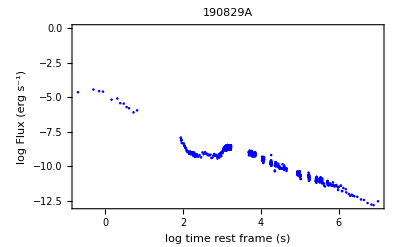

```mathematica
Loading["190829A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"190829A"]
```

0

6

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

----------------------------------------------

best fit parameters: {F→-9.08643,T→3.35114,α→0.929522,t→130.668}

theirs errors: {0.834884,0.896696,0.0134746,391.443}

confidence intervals: {{-9.9171,-8.25575},{2.45896,4.24332},{0.916115,0.942929},{-258.804,520.139}}

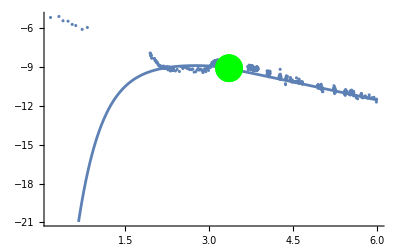

----------------------------------------------

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

GRB id afterglow has χ^2: 5.0288×10^23 and  reduced χ^2: 5.13143×10^20 α: 0

--------------testing-------------

---------------------------------

---------------------------------

NonlinearModelFit::nrlnum: The function value {Indeterminate,-1.74077×10^8,-3.22123×10^8,-3.01592×10^8,-3.80316×10^8,-4.82273×10^8,-8.56625×10^8,-4.28143×10^8,-5.80403×10^9,-8.71746×10^9,«973»} is not a list of real numbers with dimensions {983} at {T,α,t} = {6.93529,0.926751,-1265.92}.

General::munfl: Exp[-865.545] is too small to represent as a normalized machine number; precision may be lost.

NonlinearModelFit::nrlnum: The function value {Indeterminate,-1.69351×10^8,-3.13388×10^8,-2.93441×10^8,-3.70055×10^8,-4.69294×10^8,-8.33664×10^8,-4.16756×10^8,-5.66062×10^9,-8.49836×10^9,«973»} is not a list of real numbers with dimensions {983} at {T,α,t} = {6.84569,0.926819,-1231.05}.

General::munfl: Exp[-841.68] is too small to represent as a normalized machine number; precision may be lost.

NonlinearModelFit::nrlnum: The function value {Indeterminate,-1.64606×10^8,-3.04617×10^8,-2.85256×10^8,-3.59754×10^8,-4.56264×10^8,-8.1061×10^8,-4.05324×10^8,-5.51681×10^9,-8.27866×10^9,«973»} is not a list of real numbers with dimensions {983} at {T,α,t} = {6.75609,0.926889,-1196.04}.

General::stop: Further output of NonlinearModelFit::nrlnum will be suppressed during this calculation.

General::munfl: Exp[-817.718] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

leftm rightm

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
F | -9.08643 | (error , | error)
T | 3.35114 | (error , | error)
α | 0.929522 | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

```mathematica
tt=0
tf=6
Division[tt,tf]
fitowanie[-10.17,3.62,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

120922A    OK

```mathematica
Loading["120922A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"120922A"]
```

Import::nffil: File 120922A.txt not found during Import.

-Graphics-

2.85

6

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 708.051<10^T}, {Log[Times[«3»]]/Log[«1»], 708.051≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},2.85006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 708.051<10^T}, {Log[Times[«3»]]/Log[«1»], 708.051≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{0,0}},2.85006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 708.051<10.^T}, {0.434294 Log[Times[«3»]], 708.051≥10.^T}, {0., True}}],{{F,-10.3},{T,3.3},{α,1.5},{0.,0.}},2.85006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.3},{T,3.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

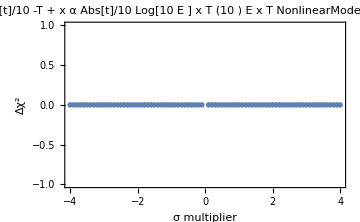
-Graphics--Graphics--Graphics-

---------------------------------

```mathematica
tt=2.85
tf=6
Division[tt,tf]
fitowanie[-10.3,3.3,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

131105A   OK

```mathematica
Loading["131105A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"131105A"]
```

Import::nffil: File 131105A.txt not found during Import.

-Graphics-

```mathematica
tt=2.6
tf=6
Division[tt,tf]
fitowanie[-10.6,3.8,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.6

6

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 398.171<10^T}, {Log[Times[«3»]]/Log[«1»], 398.171≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},2.60007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 398.171<10^T}, {Log[Times[«3»]]/Log[«1»], 398.171≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{0,0}},2.60007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 398.171<10.^T}, {0.434294 Log[Times[«3»]], 398.171≥10.^T}, {0., True}}],{{F,-10.6},{T,3.8},{α,1.5},{0.,0.}},2.60007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

140512A   OK

```mathematica
Loading["140512A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"140512A"]
```

Import::nffil: File 140512A.txt not found during Import.

-Graphics-

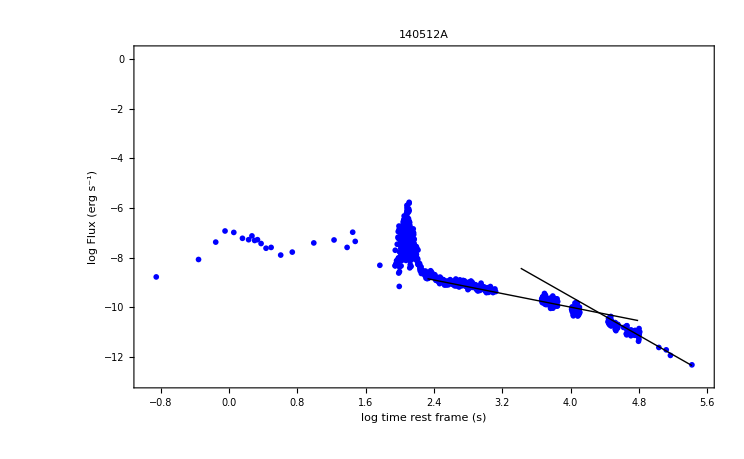

-Graphics-

```mathematica
tt=2.45
tf=5.5
Division[tt,tf]
fitowanie[-10.2,4.3,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.45

5.5

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 281.879<10^T}, {Log[Times[«3»]]/Log[«1»], 281.879≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},2.45006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 281.879<10^T}, {Log[Times[«3»]]/Log[«1»], 281.879≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{0,0}},2.45006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 281.879<10.^T}, {0.434294 Log[Times[«3»]], 281.879≥10.^T}, {0., True}}],{{F,-10.2},{T,4.3},{α,1.5},{0.,0.}},2.45006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

150403A     OK

```mathematica
Loading["150403A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"150403A"]
```

Import::nffil: File 150403A.txt not found during Import.

-Graphics-

```mathematica
tt=1.87
tf=6.15
Division[tt,tf]
fitowanie[-8.6,3,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

1.87

6.15

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 74.146<10^T}, {Log[Times[«3»]]/Log[«1»], 74.146≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},1.87009,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 74.146<10^T}, {Log[Times[«3»]]/Log[«1»], 74.146≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{0,0}},1.87009,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 74.146<10.^T}, {0.434294 Log[Times[«3»]], 74.146≥10.^T}, {0., True}}],{{F,-8.6},{T,3.},{α,1.5},{0.,0.}},1.87009,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-8.6},{T,3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

150910A     (RETRY AT tt=2.66)

```mathematica
Loading["150910A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"150910A"]
```

Import::nffil: File 150910A.txt not found during Import.

-Graphics-

```mathematica
tt=2.4
tf=5.5
Division[tt,tf]
fitowanie[-9.5,3.4,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.4

5.5

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 251.225<10^T}, {Log[Times[«3»]]/Log[«1»], 251.225≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},2.40006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 251.225<10^T}, {Log[Times[«3»]]/Log[«1»], 251.225≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{0,0}},2.40006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 251.225<10.^T}, {0.434294 Log[Times[«3»]], 251.225≥10.^T}, {0., True}}],{{F,-9.5},{T,3.4},{α,1.5},{0.,0.}},2.40006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.5},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

151027A    OK

```mathematica
Loading["151027A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"151027A"]
```

Import::nffil: File 151027A.txt not found during Import.

-Graphics-

```mathematica
tt=2.7
tf=6
Division[tt,tf]
fitowanie[-9.3,3.22,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.7

6

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 501.265<10^T}, {Log[Times[«3»]]/Log[«1»], 501.265≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},2.70007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 501.265<10^T}, {Log[Times[«3»]]/Log[«1»], 501.265≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{0,0}},2.70007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 501.265<10.^T}, {0.434294 Log[Times[«3»]], 501.265≥10.^T}, {0., True}}],{{F,-9.3},{T,3.22},{α,1.5},{0.,0.}},2.70007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.3},{T,3.22},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

160121A OK

```mathematica
Loading["160121A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"160121A"]
```

Import::nffil: File 160121A.txt not found during Import.

-Graphics-

```mathematica
tt=2.3
tf=4.6
Division[tt,tf]
fitowanie[-10.8,3.27,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.3

4.6

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 199.548<10^T}, {Log[Times[«3»]]/Log[«1»], 199.548≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},2.30005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 199.548<10^T}, {Log[Times[«3»]]/Log[«1»], 199.548≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{0,0}},2.30005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 199.548<10.^T}, {0.434294 Log[Times[«3»]], 199.548≥10.^T}, {0., True}}],{{F,-10.8},{T,3.27},{α,1.5},{0.,0.}},2.30005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

160227A    OK

```mathematica
Loading["160227A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"160227A"]
```

Import::nffil: File 160227A.txt not found during Import.

-Graphics-

```mathematica
tt=3.15
tf=6.16
Division[tt,tf]
fitowanie[-10.6,4,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

3.15

6.16

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 1412.74<10^T}, {Log[Times[«3»]]/Log[«1»], 1412.74≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},3.15006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 1412.74<10^T}, {Log[Times[«3»]]/Log[«1»], 1412.74≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{0,0}},3.15006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 1412.74<10.^T}, {0.434294 Log[Times[«3»]], 1412.74≥10.^T}, {0., True}}],{{F,-10.6},{T,4.},{α,1.5},{0.,0.}},3.15006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.6},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

160327A    OK

```mathematica
Loading["160327A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"160327A"]
```

Import::nffil: File 160327A.txt not found during Import.

-Graphics-

```mathematica
tt=2.5
tf=4.7
Division[tt,tf]
fitowanie[-10.8,3.2,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.5

4.7

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 316.26<10^T}, {Log[Times[«3»]]/Log[«1»], 316.26≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},2.50004,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 316.26<10^T}, {Log[Times[«3»]]/Log[«1»], 316.26≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{0,0}},2.50004,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 316.26<10.^T}, {0.434294 Log[Times[«3»]], 316.26≥10.^T}, {0., True}}],{{F,-10.8},{T,3.2},{α,1.5},{0.,0.}},2.50004,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

170202A     OK

```mathematica
Loading["170202A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"170202A"]
```

Import::nffil: File 170202A.txt not found during Import.

-Graphics-

```mathematica
tt=2.5
tf=5.65
Division[tt,tf]
fitowanie[-10.36,3.27,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.5

5.65

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 316.275<10^T}, {Log[Times[«3»]]/Log[«1»], 316.275≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},2.50006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 316.275<10^T}, {Log[Times[«3»]]/Log[«1»], 316.275≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{0,0}},2.50006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 316.275<10.^T}, {0.434294 Log[Times[«3»]], 316.275≥10.^T}, {0., True}}],{{F,-10.36},{T,3.27},{α,1.5},{0.,0.}},2.50006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.36},{T,3.27},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

170705A  (re-Try 4.06)

```mathematica
Loading["170705A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"170705A"]
```

Import::nffil: File 170705A.txt not found during Import.

-Graphics-

-Graphics-

```mathematica
tt=2.7
tf=6.5
Division[tt,tf]
fitowanie[-10.2,3.8,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.7

6.5

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 501.277<10^T}, {Log[Times[«3»]]/Log[«1»], 501.277≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},2.70008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 501.277<10^T}, {Log[Times[«3»]]/Log[«1»], 501.277≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{0,0}},2.70008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 501.277<10.^T}, {0.434294 Log[Times[«3»]], 501.277≥10.^T}, {0., True}}],{{F,-10.2},{T,3.8},{α,1.5},{0.,0.}},2.70008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

180329B     OK

```mathematica
Loading["180329B.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"180329B"]
```

Import::nffil: File 180329B.txt not found during Import.

-Graphics-

```mathematica
tt=2.8
tf=5.2
Division[tt,tf]
fitowanie[-10.8,3.76,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.8

5.2

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 631.029<10^T}, {Log[Times[«3»]]/Log[«1»], 631.029≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},2.80005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 631.029<10^T}, {Log[Times[«3»]]/Log[«1»], 631.029≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{0,0}},2.80005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 631.029<10.^T}, {0.434294 Log[Times[«3»]], 631.029≥10.^T}, {0., True}}],{{F,-10.8},{T,3.76},{α,1.5},{0.,0.}},2.80005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,3.76},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

190106A   OK

```mathematica
Loading["190106A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"190106A"]
```

Import::nffil: File 190106A.txt not found during Import.

-Graphics-

```mathematica
tt=2.5
tf=6.15
Division[tt,tf]
fitowanie[-10.2,4,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.5

6.15

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 316.282<10^T}, {Log[Times[«3»]]/Log[«1»], 316.282≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},2.50007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 316.282<10^T}, {Log[Times[«3»]]/Log[«1»], 316.282≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{0,0}},2.50007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 316.282<10.^T}, {0.434294 Log[Times[«3»]], 316.282≥10.^T}, {0., True}}],{{F,-10.2},{T,4.},{α,1.5},{0.,0.}},2.50007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

190114A  Retry 2.69

```mathematica
Loading["190114A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"190114A"]
```

Import::nffil: File 190114A.txt not found during Import.

-Graphics-

```mathematica
tt=2.6
tf=4.8
Division[tt,tf]
fitowanie[-10.37,3.5,1.5,0,ΔF1,Part1,tt,tf]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

2.6

4.8

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 398.148<10^T}, {Log[Times[«3»]]/Log[«1»], 398.148≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},2.60004,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 398.148<10^T}, {Log[Times[«3»]]/Log[«1»], 398.148≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{0,0}},2.60004,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 398.148<10.^T}, {0.434294 Log[Times[«3»]], 398.148≥10.^T}, {0., True}}],{{F,-10.37},{T,3.5},{α,1.5},{0.,0.}},2.60004,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.37},{T,3.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB060605  Retry 2.45

```mathematica
Loading["060605.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB060605"]

Division[2.3,5]
fitowanie[-6.73,3.58,1.5,0,ΔF1,Part1,2.3,5]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 060605.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 199.552<10^T}, {Log[Times[«3»]]/Log[«1»], 199.552≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},2.30006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 199.552<10^T}, {Log[Times[«3»]]/Log[«1»], 199.552≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{0,0}},2.30006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 199.552<10.^T}, {0.434294 Log[Times[«3»]], 199.552≥10.^T}, {0., True}}],{{F,-6.73},{T,3.58},{α,1.5},{0.,0.}},2.30006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-6.73},{T,3.58},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB060714   OK

```mathematica
Loading["060714.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB060714"]

Division[2.6,6]
fitowanie[-11.07,3.88,1.5,0,ΔF1,Part1,2.6,6]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 060714.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 398.171<10^T}, {Log[Times[«3»]]/Log[«1»], 398.171≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},2.60007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 398.171<10^T}, {Log[Times[«3»]]/Log[«1»], 398.171≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{0,0}},2.60007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 398.171<10.^T}, {0.434294 Log[Times[«3»]], 398.171≥10.^T}, {0., True}}],{{F,-11.07},{T,3.88},{α,1.5},{0.,0.}},2.60007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.07},{T,3.88},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB060814   OK

```mathematica
Loading["060814.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB060814"]

Division[2.9,6.2]
fitowanie[-10.55,3.9,1.5,0,ΔF1,Part1,2.9,6.2]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 060814.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 794.452<10^T}, {Log[Times[«3»]]/Log[«1»], 794.452≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},2.90007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 794.452<10^T}, {Log[Times[«3»]]/Log[«1»], 794.452≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{0,0}},2.90007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 794.452<10.^T}, {0.434294 Log[Times[«3»]], 794.452≥10.^T}, {0., True}}],{{F,-10.55},{T,3.9},{α,1.5},{0.,0.}},2.90007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.55},{T,3.9},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB060906 (Retry tt=2.7)

```mathematica
Loading["060906.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB060906"]

Division[3,5.5]
fitowanie[-11.7,4.3,1.5,0,ΔF1,Part1,3,5.5]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 060906.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 1000.12<10^T}, {Log[Times[«3»]]/Log[«1»], 1000.12≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},3.00005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 1000.12<10^T}, {Log[Times[«3»]]/Log[«1»], 1000.12≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{0,0}},3.00005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 1000.12<10.^T}, {0.434294 Log[Times[«3»]], 1000.12≥10.^T}, {0., True}}],{{F,-11.7},{T,4.3},{α,1.5},{0.,0.}},3.00005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.7},{T,4.3},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB061121   OK

```mathematica
Loading["061121.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB061121"]

Division[2.3,6.5]
fitowanie[-10,3.7,1.5,0,ΔF1,Part1,2.3,6.5]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 061121.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 199.566<10^T}, {Log[Times[«3»]]/Log[«1»], 199.566≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},2.30009,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 199.566<10^T}, {Log[Times[«3»]]/Log[«1»], 199.566≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{0,0}},2.30009,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 199.566<10.^T}, {0.434294 Log[Times[«3»]], 199.566≥10.^T}, {0., True}}],{{F,-10.},{T,3.7},{α,1.5},{0.,0.}},2.30009,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB061222A  Retry tt=4.1

```mathematica
Loading["061222A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB061222A"]

Division[2.4,6.3]
fitowanie[-10,4,1.5,0,ΔF1,Part1,2.4,6.3]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 061222A.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 251.235<10^T}, {Log[Times[«3»]]/Log[«1»], 251.235≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},2.40008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 251.235<10^T}, {Log[Times[«3»]]/Log[«1»], 251.235≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{0,0}},2.40008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 251.235<10.^T}, {0.434294 Log[Times[«3»]], 251.235≥10.^T}, {0., True}}],{{F,-10.},{T,4.},{α,1.5},{0.,0.}},2.40008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB070306   OK

```mathematica
Loading["070306.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB070306"]

Division[2.75,6.1]
fitowanie[-10.8,4.55,1.5,0,ΔF1,Part1,2.75,6.1]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 070306.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 562.43<10^T}, {Log[Times[«3»]]/Log[«1»], 562.43≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},2.75007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 562.43<10^T}, {Log[Times[«3»]]/Log[«1»], 562.43≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{0,0}},2.75007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 562.43<10.^T}, {0.434294 Log[Times[«3»]], 562.43≥10.^T}, {0., True}}],{{F,-10.8},{T,4.55},{α,1.5},{0.,0.}},2.75007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4.55},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB070508   Retry tt=1.94

```mathematica
Loading["070508.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB070508"]

Division[2,6]
fitowanie[-10.2,3.8,1.5,0,ΔF1,Part1,2,6]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 070508.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 100.019<10^T}, {Log[Times[«3»]]/Log[«1»], 100.019≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},2.00008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 100.019<10^T}, {Log[Times[«3»]]/Log[«1»], 100.019≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{0,0}},2.00008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 100.019<10.^T}, {0.434294 Log[Times[«3»]], 100.019≥10.^T}, {0., True}}],{{F,-10.2},{T,3.8},{α,1.5},{0.,0.}},2.00008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB080310  Retry tt=3.1

```mathematica
Loading["080310.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB080310"]

Division[3,6]
fitowanie[-11.1,4.2,1.5,0,ΔF1,Part1,3,6]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 080310.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 1000.14<10^T}, {Log[Times[«3»]]/Log[«1»], 1000.14≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},3.00006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 1000.14<10^T}, {Log[Times[«3»]]/Log[«1»], 1000.14≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{0,0}},3.00006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 1000.14<10.^T}, {0.434294 Log[Times[«3»]], 1000.14≥10.^T}, {0., True}}],{{F,-11.1},{T,4.2},{α,1.5},{0.,0.}},3.00006,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,4.2},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB080430  Retry Ta=4.8

```mathematica
Loading["080430.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB080430"]

Division[2.6,6.6]
fitowanie[-11.5,4.5,1.5,0,ΔF1,Part1,2.6,6.6]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 080430.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 398.182<10^T}, {Log[Times[«3»]]/Log[«1»], 398.182≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},2.60008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 398.182<10^T}, {Log[Times[«3»]]/Log[«1»], 398.182≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{0,0}},2.60008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 398.182<10.^T}, {0.434294 Log[Times[«3»]], 398.182≥10.^T}, {0., True}}],{{F,-11.5},{T,4.5},{α,1.5},{0.,0.}},2.60008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.5},{T,4.5},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB081008 -> to check Retry Ta=4.2

```mathematica
Loading["081008.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB081008"]

Division[3,5.5]
fitowanie[-10.8,4,1.5,0,ΔF1,Part1,3,5.5]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 081008.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 1000.12<10^T}, {Log[Times[«3»]]/Log[«1»], 1000.12≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},3.00005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 1000.12<10^T}, {Log[Times[«3»]]/Log[«1»], 1000.12≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{0,0}},3.00005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 1000.12<10.^T}, {0.434294 Log[Times[«3»]], 1000.12≥10.^T}, {0., True}}],{{F,-10.8},{T,4.},{α,1.5},{0.,0.}},3.00005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.8},{T,4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB081221   OK

```mathematica
Loading["081221.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB081221"]

Division[2.4,5.8]
fitowanie[-10.2,3.7,1.5,0,ΔF1,Part1,2.4,5.8]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 081221.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 251.229<10^T}, {Log[Times[«3»]]/Log[«1»], 251.229≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},2.40007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 251.229<10^T}, {Log[Times[«3»]]/Log[«1»], 251.229≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{0,0}},2.40007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 251.229<10.^T}, {0.434294 Log[Times[«3»]], 251.229≥10.^T}, {0., True}}],{{F,-10.2},{T,3.7},{α,1.5},{0.,0.}},2.40007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10.2},{T,3.7},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB090418A  OK

```mathematica
Loading["090418A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB090418A"]

Division[2.1,5.5]
fitowanie[-10,3.6,1.5,0,ΔF1,Part1,2.1,5.5]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 090418A.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 125.913<10^T}, {Log[Times[«3»]]/Log[«1»], 125.913≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},2.10007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 125.913<10^T}, {Log[Times[«3»]]/Log[«1»], 125.913≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{0,0}},2.10007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 125.913<10.^T}, {0.434294 Log[Times[«3»]], 125.913≥10.^T}, {0., True}}],{{F,-10.},{T,3.6},{α,1.5},{0.,0.}},2.10007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-10},{T,3.6},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB091029 Retry Tt=2.82

```mathematica
Loading["091029.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB091029"]

Division[2.7,6.4]
fitowanie[-11.1,3.8,1.5,0,ΔF1,Part1,2.7,6.4]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 091029.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 501.274<10^T}, {Log[Times[«3»]]/Log[«1»], 501.274≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},2.70008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 501.274<10^T}, {Log[Times[«3»]]/Log[«1»], 501.274≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{0,0}},2.70008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 501.274<10.^T}, {0.434294 Log[Times[«3»]], 501.274≥10.^T}, {0., True}}],{{F,-11.1},{T,3.8},{α,1.5},{0.,0.}},2.70008,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.1},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB110213A  OK

```mathematica
Loading["110213A.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB110213A"]

Division[2.3,5.8]
fitowanie[-9.4,3.4,1.5,0,ΔF1,Part1,2.3,5.8]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 110213A.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 199.559<10^T}, {Log[Times[«3»]]/Log[«1»], 199.559≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},2.30007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 199.559<10^T}, {Log[Times[«3»]]/Log[«1»], 199.559≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{0,0}},2.30007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 199.559<10.^T}, {0.434294 Log[Times[«3»]], 199.559≥10.^T}, {0., True}}],{{F,-9.4},{T,3.4},{α,1.5},{0.,0.}},2.30007,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-9.4},{T,3.4},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------

GRB120118B (Retry Tt=2.74)

```mathematica
Loading["120118B.txt"]
ListPlot[data,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->Blue,FrameLabel->{"log time rest frame (s)","log Flux (erg \!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},PlotLabel->"GRB120118B"]

Division[2.4,5]
fitowanie[-11.2,3.8,1.5,0,ΔF1,Part1,2.4,5]
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```

Import::nffil: File 120118B.txt not found during Import.

-Graphics-

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

----------------------------------------------

best fit parameters: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]

theirs errors: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterErrors]

confidence intervals: NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][ParameterConfidenceIntervals,ConfidenceLevel→0.68]

Part::partw: Part 4 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 251.219<10^T}, {Log[Times[«3»]]/Log[«1»], 251.219≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},2.40005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 251.219<10^T}, {Log[Times[«3»]]/Log[«1»], 251.219≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{0,0}},2.40005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{0.434294 Log[Times[«2»]], 251.219<10.^T}, {0.434294 Log[Times[«3»]], 251.219≥10.^T}, {0., True}}],{{F,-11.2},{T,3.8},{α,1.5},{0.,0.}},2.40005,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification BestFitParameters⟦2⟧ is longer than depth of object.

-Graphics-

----------------------------------------------

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partw: Part 3 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of NonlinearModelFit[{},Piecewise[{{Log[Power[«2»] Power[«2»]]/Log[10], 10^x<10^T}, {Log[Power[«2»] Power[«2»] Power[«2»]]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

---------------------------------

---------------------------------

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{T,3.35114},{α,0.929522},{t,130.668}},x,Weights→{}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

leftm rightm

Part::partd: Part specification NonlinearModelFit[{},Piecewise[{{Log[Times[«2»]]/Log[«1»], 10^x<10^T}, {Log[Times[«3»]]/Log[«1»], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦1,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦2,2⟧ | (error , | error)
NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,1⟧ | NonlinearModelFit[{},Piecewise[{{Log[10^F ⅇ^(α-10^(-T+x) α-10^-x Abs[t])]/Log[10], 10^x<10^T}, {Log[10^F (10^(-T+x))^-α ⅇ^(-10^-x Abs[t])]/Log[10], 10^x≥10^T}, {0, True}}],{{F,-11.2},{T,3.8},{α,1.5},{t,0}},x,Weights→{}][BestFitParameters]⟦3,2⟧ | (error , | error)

-Graphics--Graphics--Graphics-

---------------------------------